```mathematica
S1=NDSolve[{x'[τ]==-3/4 x[τ] (-1+x[τ]^2+3 y[τ]^2),y'[τ]==-1/4 y[τ] (-9+3 x[τ]^2+9 y[τ]^2+0*2 √6 x[τ]),x[0]==√0.32,y[0]==√0.68},{x,y},{τ,-10,1}];
```

```mathematica
S2=NDSolve[{x'[τ]==-3/4 x[τ] (-1+x[τ]^2+3 y[τ]^2),y'[τ]==-1/4 y[τ] (-9+3 x[τ]^2+9 y[τ]^2+0.001*2 √6 x[τ]),x[0]==√0.32,y[0]==√0.68},{x,y},{τ,-10,1}];
```

NDSolve::ndsz: At τ == -4.76421, step size is effectively zero; singularity or stiff system suspected.

```mathematica
S3=NDSolve[{x'[τ]==-3/4 x[τ] (-1+x[τ]^2+3 y[τ]^2),y'[τ]==-1/4 y[τ] (-9+3 x[τ]^2+9 y[τ]^2+0.005*2 √6 x[τ]),x[0]==√0.32,y[0]==√0.68},{x,y},{τ,-10,1}];
```

NDSolve::ndsz: At τ == -3.68955, step size is effectively zero; singularity or stiff system suspected.

```mathematica
S4=NDSolve[{x'[τ]==-3/4 x[τ] (-1+x[τ]^2+3 y[τ]^2),y'[τ]==-1/4 y[τ] (-9+3 x[τ]^2+9 y[τ]^2+0.01*2 √6 x[τ]),x[0]==√0.32,y[0]==√0.68},{x,y},{τ,-10,1}];
```

NDSolve::ndsz: At τ == -3.22547, step size is effectively zero; singularity or stiff system suspected.

```mathematica
ParametricPlot[{Evaluate[{{Exp[-t]-1,x[t]^2}/.S1,{Exp[-t]-1,x[t]^2}/.S2,{Exp[-t]-1,x[t]^2}/.S3,{Exp[-t]-1,x[t]^2}/.S4}]},{t,-5,1},PlotRange->{{0,2},{0,1}},PlotLegends->{"β=0","β=0.01","β=0.05","β=0.1"},AxesLabel->{HoldForm[z],HoldForm["x^2"]},LabelStyle->{FontFamily->"Latin Modern Mono",10,GrayLevel[0]},PlotStyle-> {Dashed,Green,Red,Yellow}]
```

InterpolatingFunction::dmval: Input value {-9.99978} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

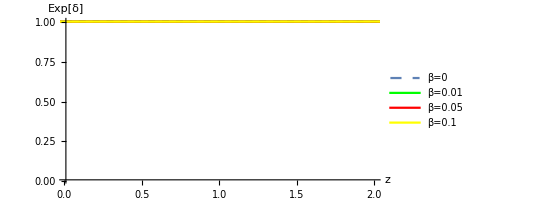

```mathematica
ParametricPlot[{Evaluate[{{Exp[-t]-1,Exp[((1-y[t]^2)/(2 x[t]^2)-1/2)^2]}/.S1,{Exp[-t]-1,Exp[((1-y[t]^2)/(2 x[t]^2)-1/2)^2]}/.S2,{Exp[-t]-1,Exp[((1-y[t]^2)/(2 x[t]^2)-1/2)^2]}/.S3,{Exp[-t]-1,Exp[((1-y[t]^2)/(2 x[t]^2)-1/2)^2]}/.S4}]},{t,-10,1},PlotRange->{{0.01,2},{0.01,1}},PlotLegends->{"β=0","β=0.01","β=0.05","β=0.1"},AxesLabel->{HoldForm[z],HoldForm["Exp[δ]"]},LabelStyle->{FontFamily->"Latin Modern Mono",10,GrayLevel[0]},PlotStyle-> {Dashed,Green,Red,Yellow}]
```

```mathematica
(1/2((1-y^2)/x^2)-1/2)x^2-y^2//FullSimplify
```

1/2 (1-x^2-3 y^2)

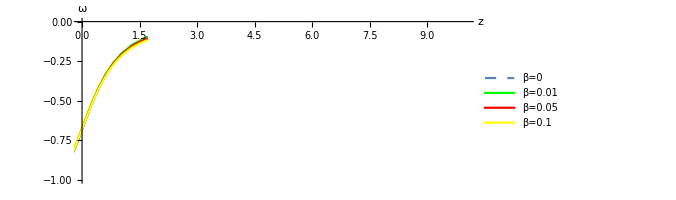

```mathematica
ParametricPlot[{Evaluate[{{Exp[-t]-1,1/2 (1-x[t]^2-3 y[t]^2)}/.S1,{Exp[-t]-1,1/2 (1-x[t]^2-3 y[t]^2)}/.S2,{Exp[-t]-1,1/2 (1-x[t]^2-3 y[t]^2)}/.S3,{Exp[-t]-1,1/2 (1-x[t]^2-3 y[t]^2)}/.S4}]},{t,-1,10},PlotRange->{{0,10},{-1,0}},PlotLegends->{"β=0","β=0.01","β=0.05","β=0.1"},AxesLabel->{HoldForm[z],HoldForm["ω"]},LabelStyle->{FontFamily->"Latin Modern Mono",10,GrayLevel[0]},PlotStyle-> {Dashed,Green,Red,Yellow}]
```

InterpolatingFunction::dmval: Input value {-4.9999} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

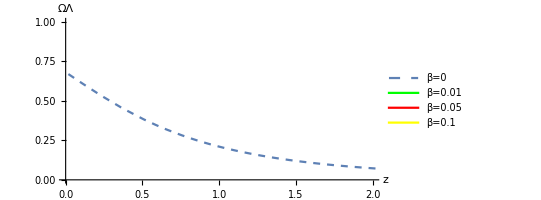

```mathematica
ParametricPlot[{Evaluate[{{Exp[-t]-1,y[t]^2}/.S1,{Exp[-t]-1,y[t]^2}/.S2,{Exp[-t]-1,y[t]^2}/.S3,{Exp[-t]-1,y[t]^2}/.S4}]},{t,-5,0},PlotRange->{{0,2},{0,1}},PlotLegends->{"β=0","β=0.01","β=0.05","β=0.1"},AxesLabel->{HoldForm[z],HoldForm["ΩΛ"]},LabelStyle->{FontFamily->"Latin Modern Mono",10,GrayLevel[0]},PlotStyle-> {Dashed,Green,Red,Yellow}]
```

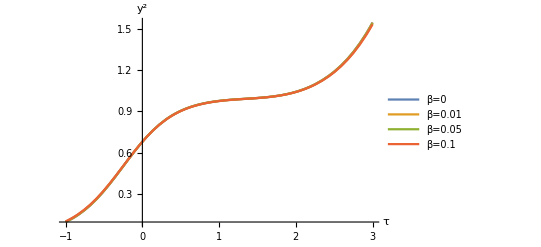

```mathematica
Plot[{Evaluate[{y[τ]^2/.S1,y[τ]^2/.S2,y[τ]^2/.S3,y[τ]^2/.S4}]},{τ,-1,3},PlotRange->All,PlotLegends->{"β=0","β=0.01","β=0.05","β=0.1"},AxesLabel->{HoldForm[τ],HoldForm["y^2"]},LabelStyle->{FontFamily->"Latin Modern Mono",10,GrayLevel[0]}]
```

InterpolatingFunction::dmval: Input value {-9.99978} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

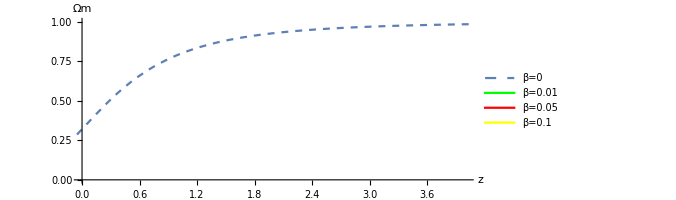

```mathematica
ParametricPlot[{Evaluate[{{Exp[-t]-1,x[t]^2}/.S1,{Exp[-t]-1,x[t]^2}/.S2,{Exp[-t]-1,x[t]^2}/.S3,{Exp[-t]-1,x[t]^2}/.S4}]},{t,-10,1},PlotRange->{{0,4},{0,1}},PlotLegends->{"β=0","β=0.01","β=0.05","β=0.1"},AxesLabel->{HoldForm[z],HoldForm["Ωm"]},LabelStyle->{FontFamily->"Latin Modern Mono",10,GrayLevel[0]},PlotStyle-> {Dashed,Green,Red,Yellow}]
```

InterpolatingFunction::dmval: Input value {-9.99959} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

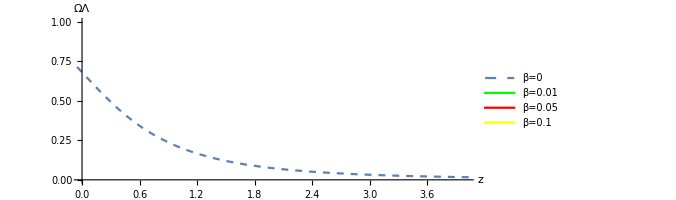

```mathematica
ParametricPlot[{Evaluate[{{Exp[-t]-1,y[t]^2}/.S1,{Exp[-t]-1,y[t]^2}/.S2,{Exp[-t]-1,y[t]^2}/.S3,{Exp[-t]-1,y[t]^2}/.S4}]},{t,-10,10},PlotRange->{{0,4},{0,1}},PlotLegends->{"β=0","β=0.01","β=0.05","β=0.1"},AxesLabel->{HoldForm[z],HoldForm["ΩΛ"]},LabelStyle->{FontFamily->"Latin Modern Mono",10,GrayLevel[0]},PlotStyle-> {Dashed,Green,Red,Yellow}]
```